Pontos de Lagrange calculados:

Ponto | Coordenadas (x,y)
L₁ | 0.82612531559464873055624862434101497200402983846539
0
L₂ | 1.1556938315211141885932939290965517545385760145435
0
L₃ | -1.0181000108426904083024343741489648006148095065393
0
L₄ | 0.487846380859127882695377240150014105038996634448109
(√3)/2
L₅ | 0.487846380859127882695377240150014105038996634448109
-(√3)/2

Gráfico salvo em: C:\Users\DELL\Desktop\LagrangePoints_ModifiedPotential.pdf

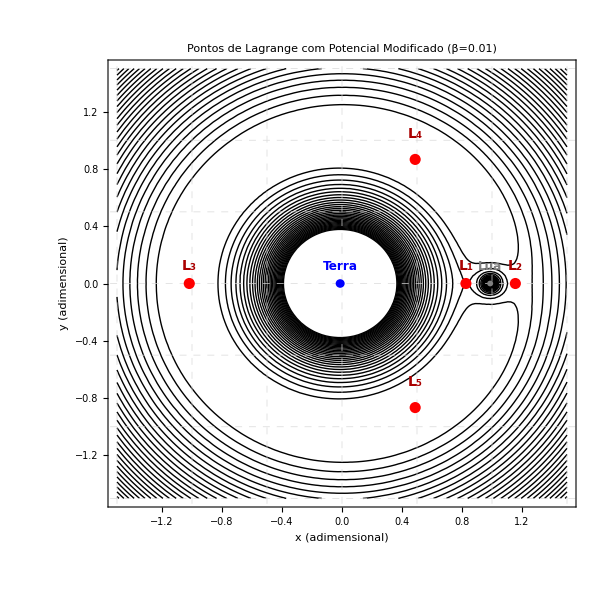

```mathematica
(*Definição de parâmetros com alta precisão*)EarthMass=5.97219`50*10^24;    (*Massa da Terra em kg*)
MoonMass=7.34767309`50*10^22;   (*Massa da Lua em kg*)
mu=SetPrecision[MoonMass/(EarthMass+MoonMass),50];
beta=SetPrecision[0.01,50];     (*Parâmetro de modificação*)

(*Funções auxiliares com potencial modificado*)
d1[x_,y_]:=Sqrt[(x+mu)^2+y^2];
d2[x_,y_]:=Sqrt[(x-(1-mu))^2+y^2];

(*Potencial modificado U(x,y)*)
U[x_,y_]:=-((1-mu)/d1[x,y]*(1+2*beta/d1[x,y]))-(mu/d2[x,y]*(1+2*beta/d2[x,y]))-(1/2)*(x^2+y^2);

(*Derivada do potencial em relação a x (y=0)*)
dUx[x_]:=Module[{},-(1/2) (2 x)+(1-mu) (1+(2 beta)/Sqrt[(mu+x)^2]) (mu+x)/((mu+x)^2)^(3/2)-(1-mu) (2 beta (mu+x)^2)/((mu+x)^2)^(5/2)+mu (1+(2 beta)/Sqrt[(-1+mu+x)^2]) (-1+mu+x)/((-1+mu+x)^2)^(3/2)-mu (2 beta (-1+mu+x)^2)/((-1+mu+x)^2)^(5/2)];

(*Cálculo preciso dos pontos de Lagrange colineares*)
L1Solution=FindRoot[dUx[x]==0,{x,1-mu-0.1`50},WorkingPrecision->50,MaxIterations->1000];
L2Solution=FindRoot[dUx[x]==0,{x,1-mu+0.1`50},WorkingPrecision->50,MaxIterations->1000];
L3Solution=FindRoot[dUx[x]==0,{x,-mu-1`50},WorkingPrecision->50,MaxIterations->1000];

(*Pontos de Lagrange*)
LagrangePoints={{"L₁",{x/. L1Solution,0}},{"L₂",{x/. L2Solution,0}},{"L₃",{x/. L3Solution,0}},{"L₄",{1/2-mu,Sqrt[3]/2}},{"L₅",{1/2-mu,-Sqrt[3]/2}}};

(*Visualização profissional*)
lagrangePlot=Show[ContourPlot[U[x,y],{x,-1.5,1.5},{y,-1.5,1.5},Contours->30,ContourShading->None,ContourStyle->Directive[Black,Thin],PlotRange->{{-1.5,1.5},{-1.5,1.5}},ColorFunction->"TemperatureMap"],Graphics[{{Blue,Disk[{-mu,0},0.03],Text[Style["Terra",12,Bold,FontFamily->"Times"],{-mu,0.12}]},{Gray,Disk[{1-mu,0},0.02],Text[Style["Lua",12,Bold,FontFamily->"Times"],{1-mu,0.12}]},{Red,AbsolutePointSize[8],Point[#[[2]]&/@LagrangePoints]},(*Correção aplicada aqui-fechamento correto dos colchetes*)MapThread[Text[Style[#1,14,Bold,Darker[Red],FontFamily->"Times"],{#2[[1]],#2[[2]]+If[#2[[2]]==0,0.12,0.18]}]&,{First/@LagrangePoints,Last/@LagrangePoints}]}],Frame->True,FrameLabel->{Style["x (adimensional)",14,FontFamily->"Times"],Style["y (adimensional)",14,FontFamily->"Times"]},PlotLabel->Style["Pontos de Lagrange com Potencial Modificado (β=0.01)",16,Bold,FontFamily->"Times"],GridLines->{Range[-1.5,1.5,0.5],Range[-1.5,1.5,0.5]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->600,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Directive[Black,Thick]];

(*Exportação*)
desktopPath=FileNameJoin[{$HomeDirectory,"Desktop"}];
Export[FileNameJoin[{desktopPath,"LagrangePoints_ModifiedPotential.pdf"}],lagrangePlot,ImageResolution->600];
Export[FileNameJoin[{desktopPath,"LagrangePoints_ModifiedPotential.png"}],lagrangePlot,ImageResolution->300];

(*Exibição dos resultados*)
Print["Pontos de Lagrange calculados:"];
Print[TableForm[LagrangePoints,TableHeadings->{None,{"Ponto","Coordenadas (x,y)"}}]];
Print["Gráfico salvo em: ",FileNameJoin[{desktopPath,"LagrangePoints_ModifiedPotential.pdf"}]];

lagrangePlot
```